```mathematica
f[x]==1/(1+f[x])
```

```mathematica
f[x]==1/(1+f[x])
```

```mathematica
f[x]==1/(1+f[x-1])
```

f[x]==1/(1+f[-1+x])

```mathematica
Reduce[f[x]==1/(1+f[-1+x])]
```

f[x]≠0&&f[-1+x]==(1-f[x])/f[x]

```mathematica
RSolve[{f[n]==1/(1+f[n-1]),f[n]==1},f[n],n]
```

RSolve::overdet: There are fewer dependent variables than equations, so the system is overdetermined.

RSolve[{f[n]==1/(1+f[-1+n]),f[n]==1},f[n],n]

```mathematica
RSolve[{f[n]==1/(1+f[n-1]),f[1]==1},f[n],n]
```

{{f[n]→-(2^(1+n) (1+√5)^-n ((1/2 (1-√5))^n-(1/2 (1+√5))^n))/(1+√5-((1-√5)/(1+√5))^n+√5 ((1-√5)/(1+√5))^n)}}

```mathematica
{{f[n]->-(2^(1+n) (1+√5)^-n ((1/2 (1-√5))^n-(1/2 (1+√5))^n))/(1+√5-((1-√5)/(1+√5))^n+√5 ((1-√5)/(1+√5))^n)}}⟦1,1,2⟧
```

-(2^(1+n) (1+√5)^-n ((1/2 (1-√5))^n-(1/2 (1+√5))^n))/(1+√5-((1-√5)/(1+√5))^n+√5 ((1-√5)/(1+√5))^n)

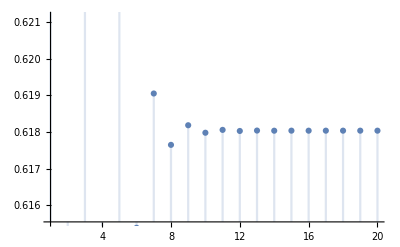

```mathematica
DiscretePlot[-(2^(1+n) (1+√5)^-n ((1/2 (1-√5))^n-(1/2 (1+√5))^n))/(1+√5-((1-√5)/(1+√5))^n+√5 ((1-√5)/(1+√5))^n),{n,1,20}]
```

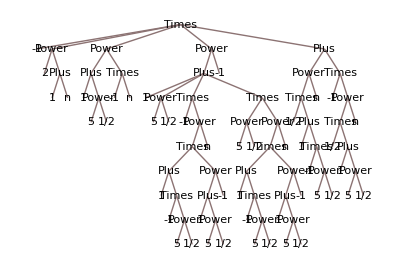

```mathematica
TreeForm[-(2^(1+n) (1+√5)^-n ((1/2 (1-√5))^n-(1/2 (1+√5))^n))/(1+√5-((1-√5)/(1+√5))^n+√5 ((1-√5)/(1+√5))^n)]
```

```mathematica
RSolve[{f[n]==1/(1+f[n-1]),f[1]==1},f[n],n]
```

{{f[n]→-(2^(1+n) (1+√5)^-n ((1/2 (1-√5))^n-(1/2 (1+√5))^n))/(1+√5-((1-√5)/(1+√5))^n+√5 ((1-√5)/(1+√5))^n)}}

```mathematica
RSolve[{f[n]==1/(1+f[n-1]),f[0]==1},f[n],n]
```

{{f[n]→(-(1-√5)^n+√5 (1-√5)^n+(1+√5)^n+√5 (1+√5)^n)/(-3 (1-√5)^n+√5 (1-√5)^n+3 (1+√5)^n+√5 (1+√5)^n)}}

```mathematica
x==1+1/(2+x)
```

x==1+1/(2+x)

```mathematica
x==1+1/(1+x)
```

x==1+1/(1+x)

```mathematica
Reduce[x==1+1/(1+x)]
```

x==-√2||x==√2

```mathematica
InputForm[Out[13]]
```

x == -Sqrt[2] || x == Sqrt[2]

```mathematica
FullForm[Out[13]]
```

Or[Equal[x,Times[-1,Power[2,Rational[1,2]]]],Equal[x,Power[2,Rational[1,2]]]]

```mathematica
x-1==1/(1+x)
```

-1+x==1/(1+x)

```mathematica
Reduce[-1+x==1/(1+x)]
```

x==-√2||x==√2

```mathematica
x==1/(2+x)
```

x==1/(2+x)

```mathematica
Reduce[x==1/(2+x)]
```

x==-1-√2||x==-1+√2

```mathematica
x==1/(2+1/(1+1/(3+1/(1+1/(8+x)))))
```

x==1/(2+1/(1+1/(3+1/(1+1/(8+x)))))

```mathematica
Reduce[x==1/(2+1/(1+1/(3+1/(1+1/(8+x)))))]
```

x==1/14 (-59-√4097)||x==1/14 (-59+√4097)

```mathematica
NestList[Sin,θ,5]
```

{θ,Sin[θ],Sin[Sin[θ]],Sin[Sin[Sin[θ]]],Sin[Sin[Sin[Sin[θ]]]],Sin[Sin[Sin[Sin[Sin[θ]]]]]}

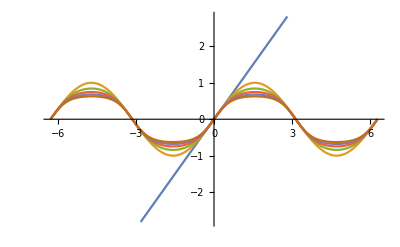

```mathematica
Plot[Out[22],{θ,-2π,2π}]
```

```mathematica
Sin[Sin[θ]]==λ Sin[θ]
```

Sin[Sin[θ]]==λ Sin[θ]

```mathematica
SolveAlways[Sin[Sin[θ]]==λ Sin[θ],{θ}]
```

SolveAlways::ifun: Inverse functions are being used by SolveAlways, so some solutions may not be found; use Reduce for complete solution information.

{{}}

```mathematica
Sin[Sin[θ]]/Sin[θ]
```

Csc[θ] Sin[Sin[θ]]

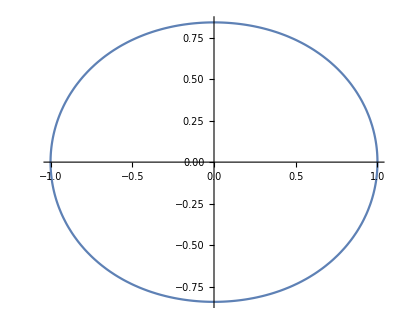

```mathematica
PolarPlot[Csc[θ] Sin[Sin[θ]],{θ,0,2 π}]
```

```mathematica
FullSimplify[Normalize[D[{x,x},x]].Normalize[D[{x,x^2},x]],x∈Reals]
```

(1+2 x)/(√(2+8 x^2))

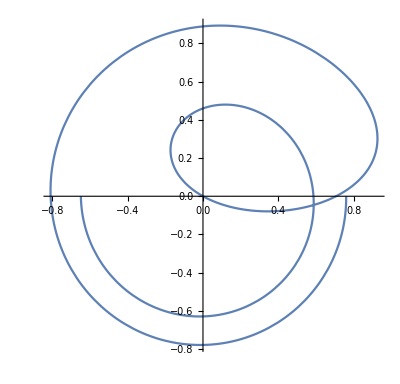

```mathematica
PolarPlot[(1+2 x)/(√(2+8 x^2)),{x,-2π,2π}]
```

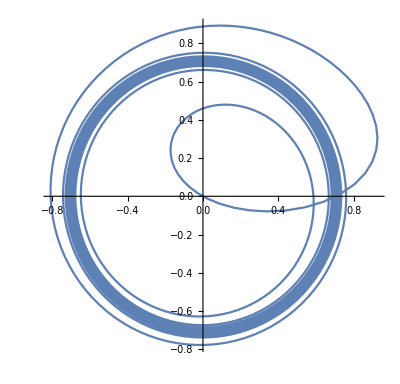

```mathematica
PolarPlot[(1+2 x)/(√(2+8 x^2)),{x,-100,100}]
```

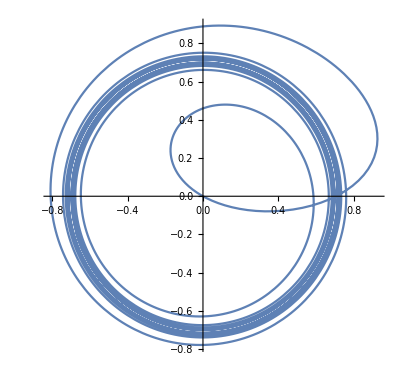

```mathematica
PolarPlot[(1+2 x)/(√(2+8 x^2)),{x,-50,50}]
```

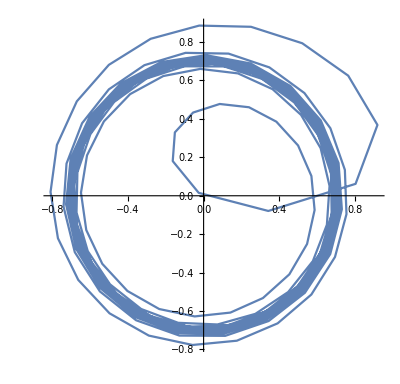

```mathematica
PolarPlot[(1+2 x)/(√(2+8 x^2)),{x,-500,500}]
```

```mathematica
FullSimplify[ArcCurvature[{x,x^3},x],x∈Reals]
```

(6 Abs[x])/((1+9 x^4)^(3/2))

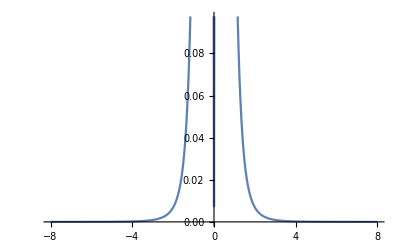

```mathematica
Plot[(6 Abs[x])/((1+9 x^4)^(3/2)),{x,-8,8}]
```

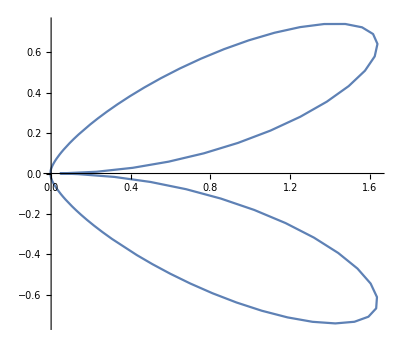

```mathematica
PolarPlot[(6 Abs[x])/((1+9 x^4)^(3/2)),{x,-50,50}]
```

```mathematica
PolarPlot[(6 Abs[x])/((1+9 x^4)^(3/2)),x∈Disk[]]
```

PolarPlot::idomdim: x∈Disk[] does not have a valid dimension as a plotting domain.

PolarPlot[(6 Abs[x])/((1+9 x^4)^(3/2)),x∈Disk[]]

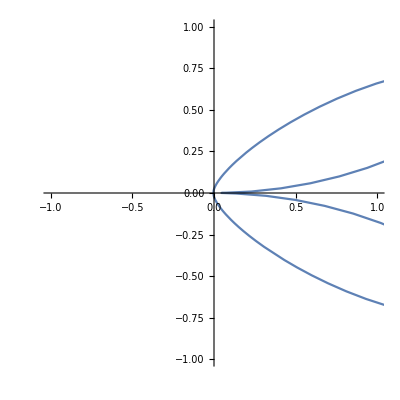

```mathematica
PolarPlot[(6 Abs[x])/((1+9 x^4)^(3/2)),{x,-50,50},PlotRange->{{-1,1},{-1,1}}]
```

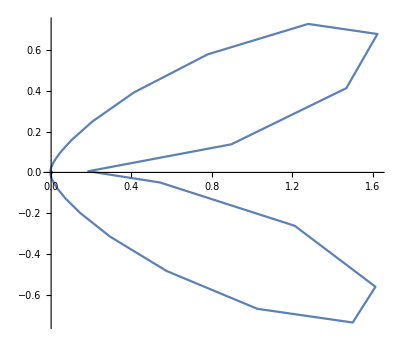

```mathematica
PolarPlot[(6 Abs[x])/((1+9 x^4)^(3/2)),{x,-200,200}]
```

```mathematica
(1+Cos[π x])/2
```

1/2 (1+Cos[π x])

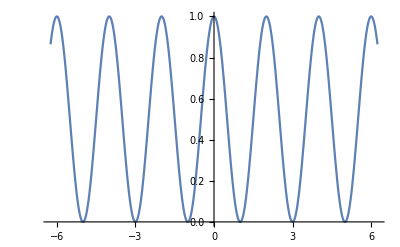

```mathematica
Plot[1/2 (1+Cos[π x]),{x,-6.24,6.24}]
```

```mathematica
(1-(1+Cos[π x])/2)(3x+1)+((1+Cos[π x])/2)x/2
```

(1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x])

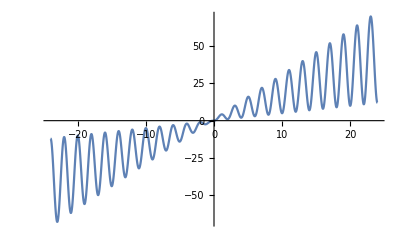

```mathematica
Plot[(1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x]),{x,-24.,24.}]
```